# Лабораторная работа №5.

Выполнила студентка ММФ БГУ 
КМ, 1 к, 5 гр. Бельская Е.А.
        30 сентября 2019

## 1. Построение дерева выражения

```mathematica
a≠0&&(x==(-b-√(b^2-4ac))/(2a))
```

```mathematica
a≠0&&x==(-b-√(-4 ac+b^2))/(2 a)
```

a≠0&&x==(-b-√(-4 ac+b^2))/(2 a)

```mathematica
ExprAsTree[expr_,options___Rule]:=Graphics[ExprAsTree[expr,{0,0}],options]
```

```mathematica
ExprAsTree[atom_?AtomQ,coord:{_,_}]:=Text[atom,coord]
```

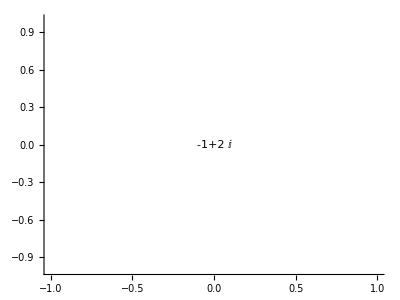

```mathematica
ExprAsTree[-1+2ⅈ,Axes->True,BaseStyle->{Large,FontWeight->Bold}]
```

```mathematica
ExprAsTree[expr_,{x_,y_}]:=Text[Head[expr],{x,y}]
```

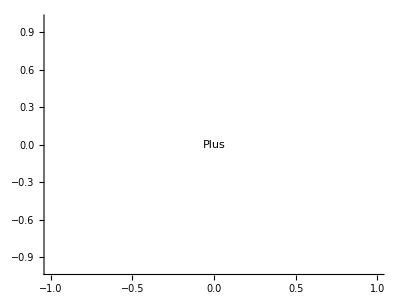

```mathematica
ExprAsTree[a+2ⅈ,Axes->True,BaseStyle->{Large,FontWeight->Bold}]
```

```mathematica
?ExprAsTree
```

Global`ExprAsTree

ExprAsTree[expr_,options___Rule]:=Graphics[ExprAsTree[expr,{0,0}],options]
 
ExprAsTree[atom_?AtomQ,Null]:=Text[atom,coord]
 
ExprAsTree[atom_?AtomQ,coord:{_,_}]:=Text[atom,coord]
 
ExprAsTree[expr_,{x_,y_}]:=Text[Head[expr],{x,y}]

```mathematica
ClearAll[Width];
```

```mathematica
Width[_?AtomQ]=1;
```

```mathematica
Width[expr_]:=Plus@@Width/@List@@(expr)
```

```mathematica
expr=1/(a^5+b)-x^9+57-v
```

57+1/(a^5+b)-v-x^9

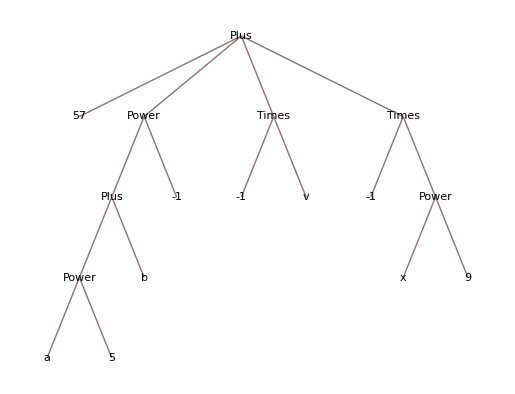

```mathematica
expr//TreeForm
```

```mathematica
Width/@List@@(expr)
```

{1,4,2,3}

```mathematica
FoldList[Plus,0,Width/@List@@(expr)]//Most
```

{0,1,5,7}

```mathematica
{x+#, y-1}&/@FoldList[Plus,0,Width/@List@@(expr)]//Most
```

{{x,-1+y},{1+x,-1+y},{5+x,-1+y},{7+x,-1+y}}

```mathematica
NodesCoord[x_,y_]:={x+#, y-1}&/@FoldList[Plus,0,Width/@List@@(expr)]//Most
```

```mathematica
MapThread[Text[#1,#2]&,{Level[expr,1],NodesCoord[x,y]}]
```

{Text[57,{x,-1+y}],Text[1/(a^5+b),{1+x,-1+y}],Text[-v,{5+x,-1+y}],Text[-x^9,{7+x,-1+y}]}

```mathematica
ExprAsTree[expr_,{x_,y_}]:={{Orange,Line[{{x,y},#}]&/@Most[{x+#, y-1}&/@FoldList[Plus, 0, Width/@List@@expr]]},Text[Tooltip[Head[expr]],{x,y},Background->LightGreen],MapThread[ExprAsTree[#1,#2]&,{Level[expr,1],{x+#, y-1}&/@FoldList[Plus,0,Width/@List@@(expr)]//Most}]}
```

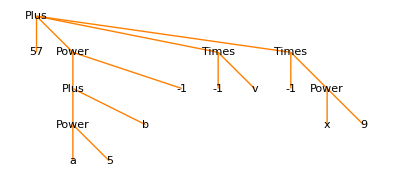

```mathematica
ExprAsTree[expr,BaseStyle->{Medium,FontWeight->Bold}]
```

```mathematica
Length[expr]
```

4

```mathematica
ExprAsTree[expr_,{x_,y_}]:={{Orange,Line[{{x,y},#}]&/@Most[{x+#, y-1}&/@FoldList[Plus, 0, Width/@List@@expr]]},Text[Head[expr],{x,y},Background->LightGreen],MapThread[ExprAsTree[#1,#2]&,{Level[expr,1],{x+#, y-1}&/@FoldList[Plus,-2.7,Width/@List@@(expr)]//Most}]}
```

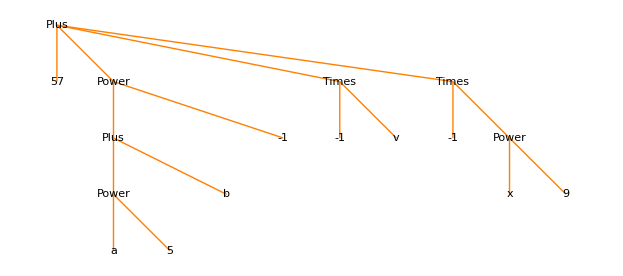

```mathematica
ExprAsTree[expr,BaseStyle->{Medium,FontWeight->Bold}]
```

## Задание 2

```mathematica
myFib1[1]:=1
```

```mathematica
myFib1[2]:=1
```

```mathematica
myFib1[n_]:=myFib1[n-1]+myFib1[n-2]
```

```mathematica
myFib1[20]
```

6765

### Задание 1.2

```mathematica
Ackerman[0,0]=1;
```

```mathematica
Ackerman[0,n_Integer]:=n+1;
Ackerman[m_Integer,0]:=Ackerman[m-1,1];
Ackerman[m_Integer, n_Integer]:=Ackerman[m,n]=Ackerman[m-1, Ackerman[m,n-1]]
```

```mathematica
Ackerman[2,3]
```

9

```mathematica
?Ackerman
```

Global`Ackerman

Ackerman[0,0]=1
 
Ackerman[1,1]=3
 
Ackerman[1,2]=4
 
Ackerman[1,3]=5
 
Ackerman[1,4]=6
 
Ackerman[1,5]=7
 
Ackerman[1,6]=8
 
Ackerman[1,7]=9
 
Ackerman[2,1]=5
 
Ackerman[2,2]=7
 
Ackerman[2,3]=9
 
Ackerman[0,n_Integer]:=n+1
 
Ackerman[m_Integer,0]:=Ackerman[m-1,1]
 
Ackerman[m_Integer,n_Integer]:=Ackerman[m,n]=Ackerman[m-1,Ackerman[m,n-1]]

```mathematica
List[Ackerman[1,#]&/@Range[5]]
```

{{3,4,5,6,7}}

```mathematica
data=Table[Ackerman[m,n],{m,0,3},{n,0,3}];
```

```mathematica
ListPlot3D[data,Mesh->All]
```

-Graphics3D-